4.

0.1

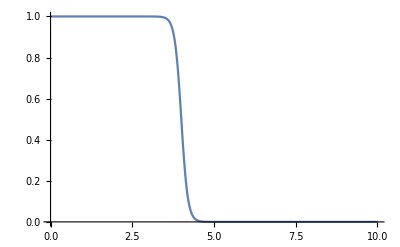

```mathematica
T0=4.
dx=0.1
(*f[x_]:=(Exp[x-Subscript[x, 0]]-0)*)
f[x_]:=(Exp[(x-T0)/dx]+1)^-1

Plot[f[x], {x, 0,10}]
```